# Simulating Data of form {th1, th2, w1, w2, a1, a2}

This worksheet simulates the SHO and coupled SHO to generate th1, th2 etc but then also uses this ‘perfect’ solution to EL to find out w1, w2 etc and save them off to a data file. This way the errors associated with a discrete differential are avoided.

```mathematica
Needs["VariationalMethods`"]
```

```mathematica
SetDirectory["Documents/Imperial/Year_4/Masters_Project/Code/Goliath/resources"];
```

## SHO oscillator

```mathematica
L[th1_, w1_]:= w1^2 - th1^2;
```

Generate the Euler Equations

```mathematica
sol=EulerEquations[L[th1[t],  D[th1[t],t]], th1[t], t]
```

-2 (th1''(t)+th1(t))==0

```mathematica
sol1=NDSolve[{sol, th1[0]==1, th1[1]==1}, th1[t], {t,0,10.0}]
```

{{th1(t)→InterpolatingFunction[{{0., 10.}}, <>](t)}}

```mathematica
deltat = 0.1;
```

```mathematica
times = Range[0,10, deltat];
```

```mathematica
expth1 = Flatten[(th1[t]/.sol1)/.t->times];
```

```mathematica
expw1 = Flatten[D[(th1[t]/.sol1), t]/.t->times];
expa1 = Flatten[D[D[(th1[t]/.sol1), t], t]/.t->times];
```

```mathematica
results=Transpose[{expth1, expw1, expa1}];
```

```mathematica
Export["sho_0.1_sim.csv", results, "CSV"];
```

## Coupled SHO

```mathematica
L1[th1_, th2_,  w1_, w2_]:= w1^2 + w2^2 - 2 th1^2 -  th2^2 + 2 th1 th2;
```

Generate the Euler Equations

```mathematica
sol2=EulerEquations[L1[th1[t], th2[t],  D[th1[t],t], D[th2[t],t] ], {th1[t], th2[t]}, t]
```

EulerEquations(L1(th1(t),th2(t),th1'(t),th2'(t)),{th1(t),th2(t)},t)

```mathematica
sol3=NDSolve[{sol2, th1[0]==1, th1[1]==1, th2[0]== 2, th2[1]== 1}, {th1[t], th2[t]}, {t,0,10.0}]
```

{{th1(t)→InterpolatingFunction[{{0., 10.}}, <>](t),th2(t)→InterpolatingFunction[{{0., 10.}}, <>](t)}}

```mathematica
deltat1 = 0.01
```

0.01

```mathematica
times1= Range[0,10, deltat1];
```

```mathematica
expth11 = Flatten[(th1[t]/.sol3)/.t->times1];
```

```mathematica
expth12 = Flatten[(th2[t]/.sol3)/.t->times1];
```

```mathematica
expw11 = Flatten[D[(th1[t]/.sol3), t]/.t->times1];
expa11 = Flatten[D[D[(th1[t]/.sol3), t], t]/.t->times1];
```

```mathematica
expw12 = Flatten[D[(th2[t]/.sol3), t]/.t->times1];
expa12 = Flatten[D[D[(th2[t]/.sol3), t], t]/.t->times1];
```

```mathematica
results1=Transpose[{expth11, expth12, expw11, expw12, expa11, expa12}];
```

```mathematica
Export["sho_coupled_0.01_sim.csv", results1, "CSV"];
```

## Pendulum Attached to a mass on a Spring

Mass M moves horizontally while attached to a spring of spring constant k. Hanging from the mass is a pendulum of arm length L and bob mass m

http://physics.ucsd.edu/students/courses/winter2008/physics110b/LECTURES/CH06_LAGRANGE.pdf

Taking m1 = 1,  m2 =1, k=1, l=1

```mathematica
L2[th_, x_, w1_, xprime_] :=  0.5*(1 + 1)*xprime^2 + 0.5*1*(1^2)*w1^2 + 1*1*Cos[th]*xprime*w1 - 0.5*1*x^2 + 1*9.81*1*Cos[th]
```

Generate the Euler Equations

```mathematica
sol4 = EulerEquations[L2[th1[t], x[t], D[th1[t],t], D[x[t],t]], {th1[t], x[t]}, t]
```

{-1. th1''(t)-cos(th1(t)) x''(t)-9.81 sin(th1(t))==0,-th1''(t) cos(th1(t))+(th1'(t))^2 sin(th1(t))-2. x''(t)-1. x(t)==0}

```mathematica
sol5 = NDSolve[{sol4, th1[0] == 2, th1[1] == 2, x[0] == 1, x[1]== 2}, {th1[t], x[t]}, {t,0,10.0}]
```

{{th1(t)→InterpolatingFunction[{{0., 10.}}, <>](t),x(t)→InterpolatingFunction[{{0., 10.}}, <>](t)}}

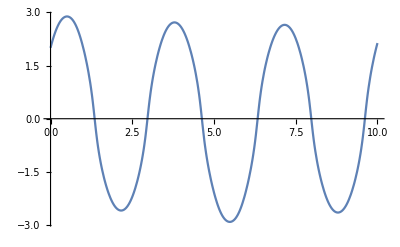

```mathematica
Plot[Evaluate[th1[t]/.sol5], {t, 0,10.0}, PlotRange->All]
```

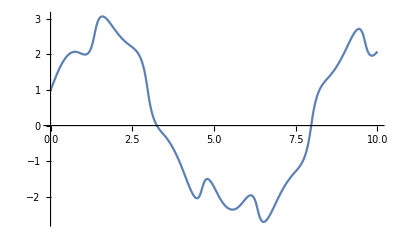

```mathematica
Plot[Evaluate[x[t]/.sol5], {t,0,10.0}, PlotRange->All]
```

```mathematica
delt = 0.1
```

0.1

```mathematica
time = Range[0, 10, delt];
```

```mathematica
datth = Flatten[(th1[t]/.sol5)/.t-> time];
```

```mathematica
datx = Flatten[(x[t]/.sol5)/.t->time];
```

```mathematica
result = Transpose[{datth, datx}];
```

Transpose::nmtx: The first two levels of {datth,datx} cannot be transposed.

```mathematica
Export["spring-pend_0.1.csv", result, "CSV"];
```

## Duffing Oscillator

Purely nonconservative system: 

-Graphics-

```mathematica
omega = 1;
lambda =  1;
n =2;
```

```mathematica
L3[x_ ,xpr_]:= 0.5*(xpr^2) - (0.5*(0.1^2)*x^2 )- (1/(1+1))*(x^(1+1));

solduff=EulerEquations[L3[x[t],  D[x[t],t]], x[t], t]
```

-1. x''(t)-1.01 x(t)==0

```mathematica
solduff2 = NDSolve[{solduff, x[0]==0, x[1]==0.1}, x[t], {t,0,10.0}]
```

{{x(t)→InterpolatingFunction[{{0., 10.}}, <>](t)}}

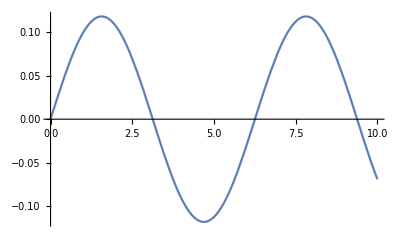

```mathematica
Plot[Evaluate[x[t]/.solduff2], {t, 0,10.0}, PlotRange->All]
```

```mathematica
delduff = 0.1;

timesduff = Range[0,10, delduff];
```

```mathematica
expxduff = Flatten[(x[t]/.solduff2)/.t->timesduff];
expxprduff = Flatten[D[(x[t]/.solduff2), t]/.t->timesduff];
expa1duff = Flatten[D[D[(x[t]/.solduff2), t], t]/.t->timesduff];
```

```mathematica
resultsduff=Transpose[{expxduff, expxprduff, expa1duff}];
```

```mathematica
Export["duff_0.1_sim.csv", resultsduff, "CSV"];
```